```mathematica
Clear[fa]
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
fa[n_, s_,x_, k_] := fa[n,s,x,k]=Sum[ -(x^(j(1-s))/j)  fa[ n/(x^j),s,x,k-1],{j,1,Log[x,n]}]
fa[n_, s_,x_, 0] := UnitStep[n-1]
fz[n_, s_,x_, z_] := Sum[ z^k / k! fa[n,s,x,k],{k,0,Log[x,n]}]
fzz[n_, s_,x_, z_] := Sum[ x^(k(1-s)) Pochhammer[-z,k]/k! ,{k,0,Log[x,n]}]
roots[n_,s_,x_]:=If[(c=Exponent[f=fzz[n,s,x,z],z])==0,{},If[c==1,List@NRoots[f==0,z][[2]],List@@NRoots[f==0,z][[All,2]]]]
rootsa[n_,s_,x_]:=If[(c=Exponent[f=fzz[n,s,x,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
proots[n_, s_, x_, z_] := Product[ 1-z/r,{r,roots[n,s,x]}]
prootsa[n_, s_, x_, z_] := Product[ 1-z/r,{r,rootsa[n,s,x]}]
srootsa[n_, s_, x_] := Sum[ -1/r,{r,rootsa[n,s,x]}]
```

```mathematica
Table[fz[n,-1,2,2],{n,2,100}]
```

{-7,-7,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9}

```mathematica
Table[fzz[n,-1,2,2],{n,2,100}]
```

{-7,-7,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9}

```mathematica
Table[fa[n,2,1],{n,2,100}]
```

{2,2,4,4,4,4,20/3,20/3,20/3,20/3,20/3,20/3,20/3,20/3,32/3,32/3,32/3,32/3,32/3,32/3,32/3,32/3,32/3,32/3,32/3,32/3,32/3,32/3,32/3,32/3,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,256/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15,416/15}

```mathematica
binomial[z_,k_]:=binomial[z,k]=Product[z-j,{j,0,k-1}]/k!
zetaHurwitz[n_,s_,y_,0]:=UnitStep[n-1]
zetaHurwitz[n_,s_,y_,1]:=zetaHurwitz[n,s,y,1]=HarmonicNumber[Floor[n],s]-HarmonicNumber[y,s]
zetaHurwitz[n_,s_,y_,2]:=zetaHurwitz[n,s,y,2]=Sum[(m^(-2s))+2(m^-s) (zetaHurwitz[Floor[n/m],s,m,1]),{m,y+1,Floor[n^(1/2)]}]
zetaHurwitz[n_,s_,y_,k_]:=zetaHurwitz[n,s,y,k]=Sum[(m^(-s k))+k(m^(-s(k-1))) zetaHurwitz[Floor[n/(m^(k-1))],s,m,1]+Sum[binomial[k,j] (m^-s)^j zetaHurwitz[Floor[n/(m^j)],s,m,k-j],{j,1,k-2}],{m,y+1,Floor[n^(1/k)]}]
zeta[n_,s_,z_]:=Expand@Sum[binomial[z,k]zetaHurwitz[n,s,1,k],{k,0,Log2@n}]

zetaAlt[n_,s_,x_,z_]:=Expand@Sum[(-1)^j binomial[z,j] x^(j(1-s))zeta[n/(x^j),s,z],{j,0,Log[x,n]}]
da[n_,x_,z_]:=zetaAlt[n,0,x,z]-zetaAlt[n-1,0,x,z]
dzz[n_,z_]:=zeta[n,0,z]-zeta[n-1,0,z]

Clear[dv]
dv[n_, x_] := dv[n,x]=- D[da[n,x,z]-dzz[n,z],{z,1}]/.z->0
```

```mathematica
Table[dv[n,2],{n,2,100}]
```

{2,0,2,0,0,0,8/3,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,32/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,32/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Clear[fv]
fv[n_, x_, k_] := fv[n,x,k]=Sum[ dv[j,x] fv[ n/j,x,k-1],{j,2,n}]
fv[n_, x_, 0] := UnitStep[n-1]
fvz[n_, x_, z_] := Sum[ z^k / k! fv[n,x,k],{k,0,Log[2,n]}]
```

```mathematica
Table[fv[32,3,k],{k,1,10}]
```

{33/2,36,27,0,0,0,0,0,0,0}

```mathematica
Table[fvz[n,3,1]-fvz[n-1,3,1],{n,2,81}]
```

{0,3,0,0,0,0,0,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,27,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,81}

```mathematica
Sum[ x^k,{k,0,Floor@Log[x,n]}]
```

(-1+x^(1+Floor[Log[n]/Log[x]]))/(-1+x)

```mathematica
x^k Pochhammer[z,k]/k!
```

```mathematica
fzz[n_, s_,x_, z_] := 1+Sum[ x^(k(1-s)) Pochhammer[z,k]/k! ,{k,1,Log[x,n]}]
fzzb[n_, x_, z_] := Table[ x^k Pochhammer[z,k]/k! ,{k,1,Log[x,n]}]
fzza[n_, x_, z_,j_] := Sum[ D[x^k Pochhammer[z,k]/k!,{z,j}]/.z->0 ,{k,1,Log[x,n]}]
```

```mathematica
Expand@fzz[100,1,2,z]
```

1+(49 z)/20+(203 z^2)/90+(49 z^3)/48+(35 z^4)/144+(7 z^5)/240+z^6/720

```mathematica
fz[100,1,2,z]
```

1+(49 z)/20+(203 z^2)/90+(49 z^3)/48+(35 z^4)/144+(7 z^5)/240+z^6/720

```mathematica
D[z(z+1)(z+2)(z+3),{z,5}]/.z->0
```

0

```mathematica
Table[ D[zetaAlt[n,0,3/2,z]-zetaAlt[n-1/2,0,3/2,z] ,z]/.z->0,{n,2,100,1/2}]
```

{1,-9/8,1,-9/8,1/2,0,1,-81/64,0,0,1,0,-569/480,0,1/2,0,0,0,1,-243/128,0,0,1,0,0,0,0,0,1/4,0,1,-2187/896,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1/2,0,-6561/2048,0,1/3,0,0,0,1,0,0,0,1,0,1/5,0,0,0,0,0,0,0,0,0,1,0,0,-2187/512,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1/2,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,-59049/10240,0,1,0,0,0,1,0,0,0,0,0,1/6,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1/4,0,0,0,1,0,0,0,0,0,0,-177147/22528,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0}

```mathematica
Sum[ x^(k(1-s))Pochhammer[-z,k]/k!,{k,0,Infinity}]
```

(1-x^(1-s))^z

```mathematica
Sum[ (-x)^(k(1-s))Pochhammer[z,k]/k!,{k,0,Infinity}]
```

(1+(-x)^-s x)^-z

```mathematica
FullSimplify@Sum[ -x^(k(1-s))/k,{k,1,Infinity}]
```

Log[1-x^(1-s)]

```mathematica
FullSimplify@Sum[ (-x^(j(1-s))/j)(-x^(k(1-s))/k),{j,1,Infinity},{k,1,Infinity}]
```

Log[1-x^(1-s)]^2

```mathematica
Sum[ z^k/k! Log[1-x^(1-s)]^k,{k,0,Infinity}]
```

(1-x^(1-s))^z

```mathematica
D[(1-x^(1-s))^z,{z,2}]/.z->0
```

Log[1-x^(1-s)]^2

```mathematica
pp[s_, x_, z_]:=(1-x^(1-s))^z
```

```mathematica
Table[{Chop@N@(fzz[100000000000,s,2,z]-pp[s,2,z])},{s,-3,3},{z,-3,3}]//Grid
```

Power::infy: Infinite expression 1/0^3 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

{1.6664×10^46} | {8.7855×10^44} | {2.37875×10^43} | {0} | {0} | {0} | {0}
{2.58775×10^35} | {1.36695×10^34} | {3.70878×10^32} | {0} | {0} | {0} | {0}
{4.34947×10^24} | {2.30871×10^23} | {6.29649×10^21} | {0} | {0} | {0} | {0}
{9.16718×10^13} | {4.9478×10^12} | {1.37439×10^11} | {0} | {0} | {0} | {0}
{ComplexInfinity} | {ComplexInfinity} | {ComplexInfinity} | {Indeterminate} | {0} | {0} | {0}
{-1.1365×10^-8} | {-5.67525×10^-10} | {0} | {0} | {0} | {0} | {0}
{0} | {0} | {0} | {0} | {0} | {0} | {0}

```mathematica
Table[{Chop@N@(fzz[100000000000,s,5,z]-pp[s,5,z])},{s,-3,3},{z,-3,3}]//Grid
```

Power::infy: Infinite expression 1/0^3 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

{1.18128×10^44} | {1.38986×10^43} | {8.68752×10^41} | {0} | {0} | {0} | {0}
{3.89283×10^33} | {4.58184×10^32} | {2.86509×10^31} | {0} | {0} | {0} | {0}
{1.31292×10^23} | {1.54816×10^22} | {9.70128×10^20} | {0} | {0} | {0} | {0}
{5.03778×10^12} | {6.00815×10^11} | {3.8147×10^10} | {0} | {0} | {0} | {0}
{ComplexInfinity} | {ComplexInfinity} | {ComplexInfinity} | {Indeterminate} | {0} | {0} | {0}
{-1.29075×10^-9} | {-1.41312×10^-10} | {0} | {0} | {0} | {0} | {0}
{0} | {0} | {0} | {0} | {0} | {0} | {0}

```mathematica
Table[{Chop@N@(fzz[10000000000000,s,1.5,z]-pp[s,1.5,z])},{s,-3,3,.5},{z,-3,3,.5}]//Grid
```

Power::infy: Infinite expression 1/0.^3. encountered.

Power::infy: Infinite expression 1/0.^2.5 encountered.

Power::infy: Infinite expression 1/0.^2. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Power::indet: Indeterminate expression 0.^0. encountered.

{9.00807×10^54} | {1.56483×10^54+0.0300619 ⅈ} | {2.40993×10^53} | {3.16102×10^52-0.122127 ⅈ} | {3.26753×10^51} | {2.15764×10^50+0.496139 ⅈ} | {0} | {-1.49323×10^48-2.01556 ⅈ} | {0} | {3.14397×10^46+8.18823 ⅈ} | {0} | {-1.11904×10^45-33.2647 ⅈ} | {0}
{3.55772×10^48} | {6.1832×10^47+0.0575335 ⅈ} | {9.52707×10^46} | {1.25025×10^46-0.180282 ⅈ} | {1.29302×10^45} | {8.54251×10^43+0.564916 ⅈ} | {0} | {-5.91817×10^41-1.77017 ⅈ} | {0} | {1.24741×10^40+5.54686 ⅈ} | {0} | {-4.44493×10^38-17.3812 ⅈ} | {0}
{1.42884×10^42} | {2.48491×10^41+0.115038 ⅈ} | {3.83133×10^40} | {5.03134×10^39-0.273215 ⅈ} | {5.2071×10^38} | {3.4426×10^37+0.648886 ⅈ} | {0} | {-2.3885×10^35-1.5411 ⅈ} | {0} | {5.04207×10^33+3.66012 ⅈ} | {0} | {-1.79951×10^32-8.69279 ⅈ} | {0}
{5.87633×10^35} | {1.02294×10^35+0.244844 ⅈ} | {1.57875×10^34} | {2.07531×10^33-0.429866 ⅈ} | {2.15×10^32} | {1.42292×10^31+0.754706 ⅈ} | {0} | {-9.89364×10^28-1.32502 ⅈ} | {0} | {2.09323×10^27+2.3263 ⅈ} | {0} | {-7.48831×10^25-4.08424 ⅈ} | {0}
{2.50378×10^29} | {4.36501×10^28+0.572433 ⅈ} | {6.74695×10^27} | {8.88281×10^26-0.715542 ⅈ} | {9.21714×10^25} | {6.11008×10^24+0.894427 ⅈ} | {0} | {-4.26274×10^22-1.11803 ⅈ} | {0} | {9.0509×10^20+1.39754 ⅈ} | {0} | {-3.25×10^19-1.74693 ⅈ} | {0}
{1.12922×10^23} | {1.9736×10^22+1.55968 ⅈ} | {3.05849×10^21} | {4.03745×10^20-1.30563 ⅈ} | {4.20091×10^19} | {2.79267×10^18+1.09297 ⅈ} | {0} | {-1.95986×10^16-0.914941 ⅈ} | {0} | {4.18747×10^14+0.765913 ⅈ} | {0} | {-1.51372×10^13-0.641159 ⅈ} | {0}
{5.64812×10^16} | {9.92171×10^15+5.65685 ⅈ} | {1.54567×10^15} | {2.05156×10^14-2.82843 ⅈ} | {2.14676×10^13} | {1.43556×10^12+1.41421 ⅈ} | {0} | {-1.02016×10^10-0.707107 ⅈ} | {0} | {2.20964×10^8+0.353553 ⅈ} | {0} | {-8.10763×10^6-0.176777 ⅈ} | {0}
{3.59417×10^10} | {6.40713×10^9+41.7614 ⅈ} | {1.01388×10^9} | {1.3684×10^8-9.38567 ⅈ} | {1.45776×10^7} | {993785.+2.10938 ⅈ} | {0} | {-7376.54-0.474073 ⅈ} | {0} | {168.38+0.106545 ⅈ} | {0} | {-6.59512-0.0239455 ⅈ} | {0}
{ComplexInfinity} | {ComplexInfinity} | {ComplexInfinity} | {ComplexInfinity} | {ComplexInfinity} | {ComplexInfinity} | {Indeterminate} | {0.0659204} | {0} | {-0.000454624} | {0} | {9.53756×10^-6} | {0}
{-0.0053359} | {-0.000891519} | {-0.000132151} | {-0.0000166954} | {-1.66333×10^-6} | {-1.05926×10^-7} | {0} | {6.83017×10^-10} | {0} | {0} | {0} | {0} | {0}
{-8.40142×10^-10} | {-1.42803×10^-10} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0}
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0}
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0}

```mathematica
N@Chop@rootsa[10000,1,2]
```

{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.}

```mathematica
pp[1.5,2,2]
```

0.0857864

```mathematica
prootsa[100000000,1,2,20]
```

0

```mathematica
fzz[1000000000,.5,2,z]
```

```mathematica
N@srootsa[1000000000,1,3/2]
```

-4.51881

```mathematica
Log[ 3/2,1000000000.]
```

51.1099

```mathematica
N@HarmonicNumber[51]
```

4.51881

```mathematica
Product[ 1-1.5/k,{k,1,Log[2,10000000000000]}]
```

-0.00100927

```mathematica
Product[ 1-(1.01+3000I)/k,{k,1,Infinity}]
```

0.

```mathematica
Clear[fob]
fob[n_, s_,x_, k_] := fob[n,s,x,k]=Sum[ -((x^(j(1-s))-1)/j)  fob[ n/(x^j),s,x,k-1],{j,1,Log[x,n]}]
fob[n_, s_,x_, 0] := UnitStep[n-1]
fobz[n_, s_,x_, z_] := Sum[ z^k / k! fob[n,s,x,k],{k,0,Log[x,n]}]
```

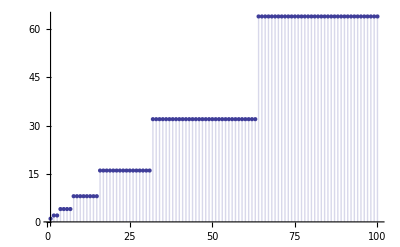

```mathematica
DiscretePlot[ fobz[n,0,2,-1],{n,1,100}]
```

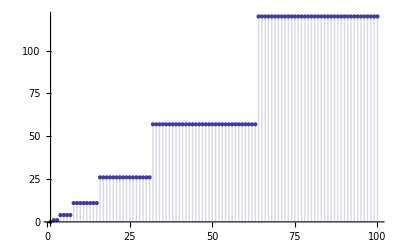

```mathematica
DiscretePlot[ fbzz[n,0,2,-1],{n,1,100}]
```

```mathematica
FullSimplify@Sum[ (-1)^(k+1)x^(k(1-s))/k,{k,1,Infinity}]
```

Log[1+x^(1-s)]

```mathematica
Sum[ Binomial[z,k] x^(k(1-s)),{k,0,Infinity}]
```

(1+x^(1-s))^z

```mathematica
FullSimplify@Sum[ x^(k(1-s))/k,{k,1,Infinity}]
```

-Log[1-x^(1-s)]

```mathematica
Sum[ z^k /(k!) (-Log[1-x^(1-s)])^k,{k,0,Infinity}]
```

(1-x^(1-s))^-z

```mathematica
(* alternating sign version *)

Clear[fc]
fc[n_, s_,x_, k_] := fc[n,s,x,k]=Sum[ (-1)^(j+1) (x^(j(1-s))/j)  fc[ n/(x^j),s,x,k-1],{j,1,Log[x,n]}]
fc[n_, s_,x_, 0] := UnitStep[n-1]
fcz[n_, s_,x_, z_] := Sum[ z^k / k! fc[n,s,x,k],{k,0,Log[x,n]}]
fczz[n_, s_,x_, z_] := Sum[ x^(k(1-s)) bin[z,k] ,{k,0,Log[x,n]}]
croots[n_,s_,x_]:=If[(c=Exponent[f=fczz[n,s,x,z],z])==0,{},If[c==1,List@NRoots[f==0,z][[2]],List@@NRoots[f==0,z][[All,2]]]]
crootsa[n_,s_,x_]:=If[(c=Exponent[f=fczz[n,s,x,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
cproots[n_, s_, x_, z_] := Product[ 1-z/r,{r,croots[n,s,x]}]
cprootsa[n_, s_, x_, z_] := Product[ 1-z/r,{r,crootsa[n,s,x]}]
csrootsa[n_, s_, x_] := Sum[ -1/r,{r,crootsa[n,s,x]}]
```

```mathematica
Table[ fcz[n,-2,2,-1],{n,1,100}]
```

{1,-7,-7,57,57,57,57,-455,-455,-455,-455,-455,-455,-455,-455,3641,3641,3641,3641,3641,3641,3641,3641,3641,3641,3641,3641,3641,3641,3641,3641,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,-29127,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017,233017}

```mathematica
Table[ fczz[n,1,2,-1],{n,1,100}]
```

{1,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
N@crootsa[10000,1,3]
```

{-0.821667-0.917058 ⅈ,-0.821667+0.917058 ⅈ,0.476791-2.88837 ⅈ,0.476791+2.88837 ⅈ,2.9943-4.8656 ⅈ,2.9943+4.8656 ⅈ,7.35057-6.40637 ⅈ,7.35057+6.40637 ⅈ}

```mathematica
fczz[100,1,2,3]
```

8

```mathematica
Chop@N@cprootsa[10000,1,2,3]
```

8.

```mathematica
Clear[foc]
foc[n_, s_,x_, k_] := foc[n,s,x,k]=Sum[ (-1)^(j+1)((x^(j(1-s))-1)/j)  foc[ n/(x^j),s,x,k-1],{j,1,Log[x,n]}]
foc[n_, s_,x_, 0] := UnitStep[n-1]
focz[n_, s_,x_, z_] := Sum[ z^k / k! foc[n,s,x,k],{k,0,Log[x,n]}]
```

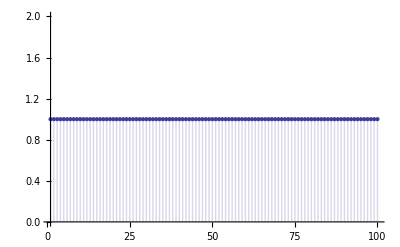

```mathematica
DiscretePlot[ focz[n,1,1.2,2],{n,1,100}]
```

```mathematica
focz[100,-1,1.2,z]
```

1+211.465 z-528.78 z^2+518.614 z^3-272.456 z^4+87.905 z^5-18.8544 z^6+2.83284 z^7-0.309427 z^8+0.0252538 z^9-0.00157225 z^10+0.0000758541 z^11-2.86984×10^-6 z^12+8.58858×10^-8 z^13-2.04509×10^-9 z^14+3.8872×10^-11 z^15-5.90156×10^-13 z^16+7.14094×10^-15 z^17-6.84929×10^-17 z^18+5.15843×10^-19 z^19-3.00514×10^-21 z^20+1.32335×10^-23 z^21-4.24849×10^-26 z^22+9.36208×10^-29 z^23-1.26368×10^-31 z^24+7.8645×10^-35 z^25

```mathematica
fob[100,1,1.2,1]
```

0.

```mathematica
Clear[fop]
fop[n_, x_, k_] := fop[n,x,k]=Sum[ -(1/j)  fop[ n/(x^j),x,k-1],{j,1,Log[x,n]}]
fop[n_, x_, 0] := UnitStep[n-1]
fopz[n_, x_, z_] := Sum[ z^k / k! fop[n,x,k],{k,0,Log[x,n]}]
fopzz[n_, x_, z_] := Sum[(-1)^k  bin[z,k],{k,0,Log[x,n]}]
parootsa[n_,x_]:=If[(c=Exponent[f=fopzz[n,x,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
pprootsa[n_, x_, z_] := Product[ 1-z/r,{r,parootsa[n,x]}]
psrootsa[n_, x_] := Sum[ -1/r,{r,parootsa[n,x]}]
```

```mathematica
Clear[foq]
foq[n_, x_, k_] := foq[n,x,k]=Sum[ (-1)^(j+1)((1)/j)  foq[ n/(x^j),x,k-1],{j,1,Log[x,n]}]
foq[n_, x_, 0] := UnitStep[n-1]
foqz[n_, x_, z_] := Sum[ z^k / k! foq[n,x,k],{k,0,Log[x,n]}]
foqzz[n_, x_, z_] := Sum[bin[z,k],{k,0,Log[x,n]}]
qrootsa[n_,x_]:=If[(c=Exponent[f=foqzz[n,x,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
qprootsa[n_, x_, z_] := Product[ 1-z/r,{r,qrootsa[n,x]}]
qsrootsa[n_, x_] := Sum[ -1/r,{r,qrootsa[n,x]}]
```

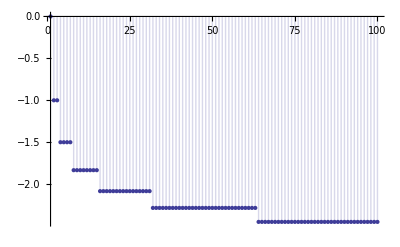

```mathematica
DiscretePlot[ fop[n,2,1],{n,1,100}]
```

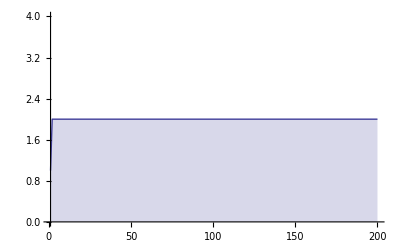

```mathematica
DiscretePlot[ foqzz[n,2,1],{n,1,200}]
```

```mathematica
Table[ FullSimplify[fopz[2^k,2,z]-fopz[2^k-1,2,z]],{k,1,5}]//TableForm
```

z
1/2 z (1+z)
1/6 z (1+z) (2+z)
1/24 z (1+z) (2+z) (3+z)
1/120 z (1+z) (2+z) (3+z) (4+z)

```mathematica
Table[ FullSimplify[fopzz[2^k,2,z]-fopzz[2^k-1,2,z]],{k,1,5}]//TableForm
```

z
1/2 z (1+z)
1/6 z (1+z) (2+z)
1/24 z (1+z) (2+z) (3+z)
1/120 z (1+z) (2+z) (3+z) (4+z)

```mathematica
Table[ FullSimplify[foqz[2^k,2,z]-foqz[2^k-1,2,z]],{k,1,5}]//TableForm
```

-z
1/2 z (1+z)
-1/6 z (1+z) (2+z)
1/24 z (1+z) (2+z) (3+z)
-1/120 z (1+z) (2+z) (3+z) (4+z)

```mathematica
Table[ FullSimplify[foqzz[2^k,2,z]-foqzz[2^k-1,2,z]],{k,1,5}]//TableForm
```

-z
1/2 z (1+z)
-1/6 z (1+z) (2+z)
1/24 z (1+z) (2+z) (3+z)
-1/120 z (1+z) (2+z) (3+z) (4+z)

```mathematica
Sum[ Pochhammer[-z,k]/k!,{k,0,Infinity}]
```

HypergeometricPFQ[{-z},{},1]

```mathematica
Sum[(-1)^k  Pochhammer[-z,k]/k!,{k,0,Infinity}]
```

2^z

```mathematica
Sum[ (-1)^k Binomial[z,k],{k,0,Infinity}]
```

HypergeometricPFQ[{-z},{},1]

```mathematica
Sum[(-1)^k  Pochhammer[z,k]/k!,{k,0,Infinity}]
```

```mathematica
N@qrootsa[100,1.2]
```

{-0.685615-1.44102 ⅈ,-0.685615+1.44102 ⅈ,0.109333-3.04474 ⅈ,0.109333+3.04474 ⅈ,1.27778-4.75948 ⅈ,1.27778+4.75948 ⅈ,2.80018-6.53172 ⅈ,2.80018+6.53172 ⅈ,4.6835-8.31832 ⅈ,4.6835+8.31832 ⅈ,6.9517-10.0774 ⅈ,6.9517+10.0774 ⅈ,9.64711-11.7615 ⅈ,9.64711+11.7615 ⅈ,12.8383-13.3094 ⅈ,12.8383+13.3094 ⅈ,16.6384-14.6322 ⅈ,16.6384+14.6322 ⅈ,21.2502-15.5833 ⅈ,21.2502+15.5833 ⅈ,27.0974-15.8805 ⅈ,27.0974+15.8805 ⅈ,35.3918-14.8102 ⅈ,35.3918+14.8102 ⅈ,-1.}

```mathematica
FullSimplify@Sum[ Pochhammer[-z,k]/k!,{k,0,n}]
```

Gamma[1+n-z]/(Gamma[1+n] Gamma[1-z])

```mathematica
Expand@Sum[ Pochhammer[-z,k]/k!,{k,0,8}]
```

1-(761 z)/280+(29531 z^2)/10080-(267 z^3)/160+(1069 z^4)/1920-(9 z^5)/80+(13 z^6)/960-z^7/1120+z^8/40320

```mathematica
Expand@Sum[(-1)^k bin[z,k],{k,0,8}]
```

1-(761 z)/280+(29531 z^2)/10080-(267 z^3)/160+(1069 z^4)/1920-(9 z^5)/80+(13 z^6)/960-z^7/1120+z^8/40320

```mathematica
Sum[(-1)^k Binomial[z,k],{k,0,n}]
```

(-1)^n Binomial[-1+z,n]

```mathematica
Expand[(-1)^n bin[-1+z,n]/.n->8]
```

1-(761 z)/280+(29531 z^2)/10080-(267 z^3)/160+(1069 z^4)/1920-(9 z^5)/80+(13 z^6)/960-z^7/1120+z^8/40320

```mathematica
FullSimplify@Sum[ Binomial[z,k],{k,0,n}]
```

```mathematica
Sum[ 1/(3j+1)+1/(3 j+2) -2/(3j +3 ),{j,0,Infinity}]
```

Log[3]

```mathematica
D[Binomial[z,3],z]/.z->0
```

1/3

```mathematica
Clear[px,py]
px[n_,k_]:=px[n,k]=Sum[(-1)^(j+1)/j px[n-j,k-1],{j,1,n-1}]
px[n_,1]:=(-1)^(n+1)/n
px[n_,0]:=0
py[n_,k_]:=py[n,k]=Sum[1/j py[n-j,k-1],{j,1,n-1}]
py[n_,1]:=1/n
py[n_,0]:=0
```

```mathematica
Table[ FullSimplify[Sum[ z^k/k! px[n,k],{k,0,n}]],{n,0,6}]//TableForm
```

0
z
1/2 (-1+z) z
1/6 (-2+z) (-1+z) z
1/24 (-3+z) (-2+z) (-1+z) z
1/120 (-4+z) (-3+z) (-2+z) (-1+z) z
1/720 (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z

```mathematica
Table[FullSimplify@Binomial[z,n],{n,0,6}]//TableForm
```

1
z
1/2 (-1+z) z
1/6 (-2+z) (-1+z) z
1/24 (-3+z) (-2+z) (-1+z) z
1/120 (-4+z) (-3+z) (-2+z) (-1+z) z
Binomial[z,6]

```mathematica
Table[ FullSimplify[Sum[  z^k/k!py[n,k],{k,0,n}]],{n,0,6}]//TableForm
```

0
z
1/2 z (1+z)
1/6 z (1+z) (2+z)
1/24 z (1+z) (2+z) (3+z)
1/120 z (1+z) (2+z) (3+z) (4+z)
1/720 z (1+z) (2+z) (3+z) (4+z) (5+z)

```mathematica
Clear[px]
t[n_, a_, b_] := b(Floor[n/b]-Floor[(n-1)/b])-a(Floor[n/a]-Floor[(n-1)/a])
px[n_,a_, b_, k_]:=px[n,k]=Sum[t[j,a,b]/j px[n-j,a,b,k-1],{j,1,n-1}]
px[n_,a_, b_, 1]:=t[n,a,b]/n
px[n_,a_, b_, 0]:=0


Table[ FullSimplify@Sum[ z^k/k! px[n,5,1,k],{k,0,n}],{n,0,6}]//TableForm
```

0
z
1/2 z (1+z)
1/6 z (1+z) (2+z)
1/24 z (1+z) (2+z) (3+z)
1/120 (-1+z) z (6+z) (16+z (5+z))
1/720 (-1+z) z (-120+z (326+z (101+z (16+z))))

```mathematica
Table[FullSimplify@( (-1)^n Pochhammer[z,n]/n!),{n,0,6}]//TableForm
```

1
-z
1/2 z (1+z)
-1/6 z (1+z) (2+z)
1/24 z (1+z) (2+z) (3+z)
-1/120 z (1+z) (2+z) (3+z) (4+z)
1/720 z (1+z) (2+z) (3+z) (4+z) (5+z)

```mathematica
Table[FullSimplify@Sum[ z^k/k! px[n,2,1,k],{k,0,n}],{n,0,6}]//TableForm
```

0
z
1/2 (-1+z) z
1/6 (-2+z) (-1+z) z
1/24 (-3+z) (-2+z) (-1+z) z
1/120 (-4+z) (-3+z) (-2+z) (-1+z) z
1/720 (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z

```mathematica
Table[FullSimplify[Expand[(Pochhammer[z,n]/n!)]],{n,0,8}]//TableForm
```

1
z
1/2 z (1+z)
1/6 z (1+z) (2+z)
1/24 z (1+z) (2+z) (3+z)
1/120 z (1+z) (2+z) (3+z) (4+z)
1/720 z (1+z) (2+z) (3+z) (4+z) (5+z)
(z (1+z) (2+z) (3+z) (4+z) (5+z) (6+z))/5040
(z (1+z) (2+z) (3+z) (4+z) (5+z) (6+z) (7+z))/40320

```mathematica
sa[n_, x_] := Sum[(-1)^(k) bin[z,k],{k,0,Log[x,n]}]
si2[n_, x_] := -Sum[ bin[z,k],{k,0,Log[x,n]}] + 2 Sum[ bin[z,2k],{k,0,Log[n]/(2Log[x])}]
```

```mathematica
Expand@sa[100,2]
```

1-(49 z)/20+(203 z^2)/90-(49 z^3)/48+(35 z^4)/144-(7 z^5)/240+z^6/720

```mathematica
Expand@si2[100,2]
```

1-(49 z)/20+(203 z^2)/90-(49 z^3)/48+(35 z^4)/144-(7 z^5)/240+z^6/720

```mathematica
sx[n_, x_] := Sum[ Pochhammer[-z,k]/k!,{k,0,Log[x,n]}]
sx2[n_, x_] := -Sum[ (-1)^k Pochhammer[-z,k]/k!,{k,0,Log[x,n]}] + 2 Sum[ (-1)^(2k)Pochhammer[-z,2k]/((2k)!),{k,0,Log[n]/(2Log[x])}]
sx2a[n_, x_] := Sum[ t[k,2,1] Pochhammer[-z,k]/k!,{k,0,Log[x,n]}] - 2 Sum[ t[2k,2,1]Pochhammer[-z,2k]/((2k)!),{k,0,Log[n]/(2Log[x])}]
sx3[n_, x_] := Sum[ t[k,3,1] Pochhammer[-z,k]/k!,{k,0,Log[x,n]}] - 3Sum[ t[3k,3,1]Pochhammer[-z,3k]/((3k)!),{k,0,Log[n]/(3Log[x])}]
```

```mathematica
FullSimplify@sx[100,2]
```

1/720 (-6+z) (-5+z) (-4+z) (-3+z) (-2+z) (-1+z)

```mathematica
FullSimplify@sx2[100,2]
```

1/720 (-6+z) (-5+z) (-4+z) (-3+z) (-2+z) (-1+z)

```mathematica
FullSimplify@sx2a[100,2]
```

1/720 (-6+z) (-5+z) (-4+z) (-3+z) (-2+z) (-1+z)

```mathematica
FullSimplify@sx3[100,2]
```

1/360 (-3+z) (-480+z (314+z (-483+z (134+z (-27+2 z)))))

```mathematica
t[0,3,1]
```

-2

```mathematica
Sum[ Pochhammer[z,k]/k!,{k,0,Infinity}]
```

HypergeometricPFQ[{z},{},1]

```mathematica
Sum[ Pochhammer[z,k]/k!,{k,0,n}]
```

((1+n) Gamma[1+n+z])/(z Gamma[2+n] Gamma[z])

```mathematica
Expand[Pochhammer[-z,k]/k!/.k->5]
```

-z/5+(5 z^2)/12-(7 z^3)/24+z^4/12-z^5/120

```mathematica
Expand[(-1)^k Binomial[z,k]/.k->5]
```

-z/5+(5 z^2)/12-(7 z^3)/24+z^4/12-z^5/120

```mathematica
Table[t[n,1,2],{n,0,10}]
```

{1,-1,1,-1,1,-1,1,-1,1,-1,1}

```mathematica
Table[ px[n,2,1,k],{n,0,9},{k,0,n}]//TableForm
```

0 |  |  |  |  |  |  |  |  | 
0 | 1 |  |  |  |  |  |  |  | 
0 | -1/2 | 1 |  |  |  |  |  |  | 
0 | 1/3 | -1 | 1 |  |  |  |  |  | 
0 | -1/4 | 11/12 | -3/2 | 1 |  |  |  |  | 
0 | 1/5 | -5/6 | 7/4 | -2 | 1 |  |  |  | 
0 | -1/6 | 137/180 | -15/8 | 17/6 | -5/2 | 1 |  |  | 
0 | 1/7 | -7/10 | 29/15 | -7/2 | 25/6 | -3 | 1 |  | 
0 | -1/8 | 363/560 | -469/240 | 967/240 | -35/6 | 23/4 | -7/2 | 1 | 
0 | 1/9 | -761/1260 | 29531/15120 | -89/20 | 1069/144 | -9 | 91/12 | -4 | 1

```mathematica
Table[ px[n,6,1,k],{n,0,9},{k,0,n}]//TableForm
```

0 |  |  |  |  |  |  |  |  | 
0 | 1 |  |  |  |  |  |  |  | 
0 | 1/2 | 1 |  |  |  |  |  |  | 
0 | 1/3 | 1 | 1 |  |  |  |  |  | 
0 | 1/4 | 11/12 | 3/2 | 1 |  |  |  |  | 
0 | 1/5 | 5/6 | 7/4 | 2 | 1 |  |  |  | 
0 | -5/6 | 137/180 | 15/8 | 17/6 | 5/2 | 1 |  |  | 
0 | 1/7 | -13/10 | 29/15 | 7/2 | 25/6 | 3 | 1 |  | 
0 | 1/8 | -197/560 | -251/240 | 967/240 | 35/6 | 23/4 | 7/2 | 1 | 
0 | 1/9 | -79/1260 | -15829/15120 | 9/20 | 1069/144 | 9 | 91/12 | 4 | 1

```mathematica
Clear[px,pxa]
t[n_, a_, b_] := b(Floor[n/b]-Floor[(n-1)/b])-a(Floor[n/a]-Floor[(n-1)/a])
px[n_,a_, b_, k_]:=px[n,a,b,k]=Sum[t[j,a,b]/j px[n-j,a,b,k-1],{j,1,n-1}]
px[n_,a_, b_, 1]:=t[n,a,b]/n
px[n_,a_, b_, 0]:=0
pxa[n_,a_, b_, k_]:=pxa[n,a,b,k]=Sum[t[j,a,b]/j pxa[n-j,a,b,k-1],{j,1,n-1}]
pxa[n_,a_, b_, 1]:=t[n,a,b]/n
pxa[n_,a_, b_, 0]:=0
```

```mathematica
Clear[pm]
pm[n_,a_, b_, k_]:=pm[n,a,b,k]=Sum[(-1)^(a j+b)/j pm[n-j,a,b,k-1],{j,1,n-1}]
pm[n_,a_, b_, 1]:=(-1)^(a n+b)/n
pm[n_,a_, b_, 0]:=0
```

```mathematica
Table[FullSimplify@Sum[ z^k/k! pm[n,0,I/2,k],{k,0,n}],{n,0,6}]//TableForm
```

0
(-1)^(ⅈ/2) z
1/2 (-1)^(ⅈ/2) z (1+(-1)^(ⅈ/2) z)
1/6 (-1)^(ⅈ/2) z (2+3 (-1)^(ⅈ/2) z+(-1)^ⅈ z^2)
1/24 (-1)^(ⅈ/2) z (1+(-1)^(ⅈ/2) z) (2+(-1)^(ⅈ/2) z) (3+(-1)^(ⅈ/2) z)
1/120 (-1)^(ⅈ/2) z (1+(-1)^(ⅈ/2) z) (2+(-1)^(ⅈ/2) z) (3+(-1)^(ⅈ/2) z) (4+(-1)^(ⅈ/2) z)
1/720 (-1)^(ⅈ/2) z (1+(-1)^(ⅈ/2) z) (2+(-1)^(ⅈ/2) z) (3+(-1)^(ⅈ/2) z) (4+(-1)^(ⅈ/2) z) (5+(-1)^(ⅈ/2) z)

```mathematica
FullSimplify[Sum[ (-1)^(k(a+b I)) Binomial[z,k],{k,0,Infinity}]]
```

(1+(-1)^(a+ⅈ b))^z

```mathematica
FullSimplify[Sum[ (-1)^(k(a+b I)) Pochhammer[-z,k]/k!,{k,0,Infinity}]]
```

(1-(-1)^(a+ⅈ b))^z

```mathematica
Clear[px,py]
px[n_,k_]:=px[n,k]=Sum[(-1)^(j+1)/j px[n-j,k-1],{j,1,n-1}]
px[n_,1]:=(-1)^(n+1)/n
px[n_,0]:=0
py[n_,k_]:=py[n,k]=If[n<1,0,Sum[1/j py[n-j,k-1],{j,1,n-1}]]
py[n_,1]:=If[n<1,0,1/n]
py[n_,0]:=0
```

```mathematica
px[100,2]
```

360968703235711654233892612988250163157207/3486018761485623858226690446765615177840000

```mathematica
Clear[px,py,pxx]
t[n_, a_, b_] := b(Floor[n/b]-Floor[(n-1)/b])-a(Floor[n/a]-Floor[(n-1)/a])
px[n_,k_]:=px[n,k]=Sum[(-1)^(j+1)/j px[n-j,k-1],{j,1,n}]
px[n_,0]:=UnitStep[n]
pxx[n_,a_,b_,k_]:=pxx[n,a,b,k]=Sum[t[j,a,b]/j pxx[n-j,a,b,k-1],{j,1,n}]
pxx[n_,a_,b_,0]:=UnitStep[n]
py[n_,k_]:=py[n,k]=If[n<1,0,Sum[1/j py[n-j,k-1],{j,1,n}]]
py[n_,0]:=UnitStep[n]
dpy[n_, k_] := py[n,k]-py[n-1,k]
pym[n_,m_,a_,b_]:=If[b==0,py[n,a],If[a==0,py[n/m,b],Sum[ dpy[j,a]dpy[k,b],{j,1,n},{k,1,(n-j)/m}]]]
pyx[n_,k_]:=Sum[ (-1)^j Binomial[k,j] pym[ n,2,k-j,j],{j,0,k}]
pyxx[n_,m_,k_]:=Sum[ (-1)^j Binomial[k,j] pym[ n,m,k-j,j],{j,0,k}]
```

```mathematica
{px[120,5],pyx[120,5]}
```

{-6766304837416110487180817591213595916178240456075784958965213649424740665222943301612996720006043424833044359/551740808903438229989722739812058181212700729612774147964353004731191621078401554848864018189373849600000000,-6766304837416110487180817591213595916178240456075784958965213649424740665222943301612996720006043424833044359/551740808903438229989722739812058181212700729612774147964353004731191621078401554848864018189373849600000000}

```mathematica
{pxx[50,4,1,4],pyxx[50,4,4]}
```

{1149514901403120187801632636324162183013/657739628513519800564069482676147200000,1149514901403120187801632636324162183013/657739628513519800564069482676147200000}

```mathematica
px[16,1]
```

95549/144144

```mathematica
py[16,1]-py[8,1]
```

95549/144144

```mathematica
px[12,2]
```

150781/207900

```mathematica
Sum[ (-1)^(j+1)/j px[12-j,1],{j,1,12}]
```

150781/207900

```mathematica
Sum[ 1/j px[12-j,1],{j,1,12}]-2Sum[ 1/(j) px[12-j,1],{j,2,12,2}]
```

150781/207900

```mathematica
Sum[ 1/j px[12-j,1],{j,1,12}]-2Sum[ 1/(2 j) px[12-2 j,1],{j,1,6}]
```

150781/207900

```mathematica
Sum[ 1/j px[12-j,1],{j,1,12}]-Sum[ 1/ j px[12-2 j,1],{j,1,6}]
```

150781/207900

```mathematica
Sum[ 1/j (py[12-j,1]-py[(12-j)/2,1]),{j,1,12}]-Sum[ 1/ j px[12-2 j,1],{j,1,6}]
```

150781/207900

```mathematica
Sum[ 1/j (py[12-j,1]-py[(12-j)/2,1]),{j,1,12}]-Sum[ 1/ j (py[12-2 j,1]-py[(6- j),1]),{j,1,6}]
```

150781/207900

```mathematica
Sum[ 1/j py[12-j,1],{j,1,12}]-Sum[ 1/j py[(12-j)/2,1],{j,1,12}]-Sum[ 1/ j py[12-2 j,1],{j,1,6}]+Sum[ 1/ j py[(6- j),1],{j,1,6}]
```

150781/207900

```mathematica
py[12,2]-Sum[ 1/j py[(12-j)/2,1],{j,1,12}]-Sum[ 1/ j py[12-2 j,1],{j,1,6}]+py[6,2]
```

150781/207900

```mathematica
py[12,2]-2Sum[ 1/j py[(12-j)/2,1],{j,1,12}]+py[6,2]
```

150781/207900

```mathematica
{Sum[ 1/j py[(12-j)/2,1],{j,1,12}],Sum[ 1/ j py[12-2 j,1],{j,1,6}], pym[12,2,1,1]}
```

{3733/630,3733/630,3733/630}

```mathematica
py[12,2]-2pym[12,2,1,1]+py[6,2]
```

150781/207900

```mathematica
{px[50,3], py[50,3]-3pym[50,2,2,1]+3pym[50,2,1,2]-py[50/2,3]}
```

{-69289605682595051818652751455399/318853045822253797241687139840000,-69289605682595051818652751455399/318853045822253797241687139840000}

```mathematica
Grid@Table[ Binomial[k,j],{k,0,8},{j,0,k}]
```

1 |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1

```mathematica
Grid@Table[Pochhammer[k,j]/j!,{k,0,8},{j,0,k}]
```

1 |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  | 
1 | 2 | 3 |  |  |  |  |  | 
1 | 3 | 6 | 10 |  |  |  |  | 
1 | 4 | 10 | 20 | 35 |  |  |  | 
1 | 5 | 15 | 35 | 70 | 126 |  |  | 
1 | 6 | 21 | 56 | 126 | 252 | 462 |  | 
1 | 7 | 28 | 84 | 210 | 462 | 924 | 1716 | 
1 | 8 | 36 | 120 | 330 | 792 | 1716 | 3432 | 6435

```mathematica
Clear[px]
t[n_, a_, b_] := b(Floor[n/b]-Floor[(n-1)/b])-a(Floor[n/a]-Floor[(n-1)/a])
px[n_,a_, b_, k_]:=px[n,a,b,k]=Sum[t[j,a,b]/j px[n-j,a,b,k-1],{j,1,n-1}]
px[n_,a_, b_, 1]:=t[n,a,b]/n
px[n_,a_, b_, 0]:=0
pz[n_, a_, b_, z_] := Sum[ z^k/k! px[n,a,b,k],{k,0,n}]
pz[n_, a_, b_,0] := 1
pz[0, a_, b_,z_] := 1
Table[ FullSimplify@pz[n,2,1,z],{n,0,6}]//TableForm
```

1
z
1/2 (-1+z) z
1/6 (-2+z) (-1+z) z
1/24 (-3+z) (-2+z) (-1+z) z
1/120 (-4+z) (-3+z) (-2+z) (-1+z) z
1/720 (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z

```mathematica
Grid@Table[pz[j,16,1,k]-pz[j,2,1,k],{k,0,11},{j,0,k}]
```

0 |  |  |  |  |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  |  |  | 
0 | 0 | 2 |  |  |  |  |  |  |  |  | 
0 | 0 | 3 | 9 |  |  |  |  |  |  |  | 
0 | 0 | 4 | 16 | 34 |  |  |  |  |  |  | 
0 | 0 | 5 | 25 | 65 | 125 |  |  |  |  |  | 
0 | 0 | 6 | 36 | 111 | 246 | 461 |  |  |  |  | 
0 | 0 | 7 | 49 | 175 | 441 | 917 | 1715 |  |  |  | 
0 | 0 | 8 | 64 | 260 | 736 | 1688 | 3424 | 6434 |  |  | 
0 | 0 | 9 | 81 | 369 | 1161 | 2919 | 6399 | 12861 | 24309 |  | 
0 | 0 | 10 | 100 | 505 | 1750 | 4795 | 11320 | 24265 | 48610 | 92377 | 
0 | 0 | 11 | 121 | 671 | 2541 | 7546 | 19118 | 43593 | 92323 | 184745 | 352715

```mathematica
FullSimplify[Pochhammer[z,k]/k!-Binomial[z,k]]
```

```mathematica
(-1)^4 Pochhammer[-13,4]/4!
```

715

```mathematica
FullSimplify[(-1)^k bin[-z,k]-bin[z,k]/.k->5]
```

1/6 z^2 (5+z^2)

```mathematica
Table[FullSimplify@Sum[pz[a,k,1,z],{k,1,10}],{a,0,10}]//TableForm
```

10
9 z
1/2 z (7+9 z)
1/2 z (1+z) (4+3 z)
1/8 z (6+z (25+z (14+3 z)))
1/120 z (96+z (170+z (255+z (70+9 z))))
1/240 z (-80+z (502+z (285+z (215+z (35+3 z)))))
(z (480+z (-224+z (3262+z (1015+z (455+z (49+3 z)))))))/1680
(z (-25200+z (35628+z (16324+z (42441+z (8680+z (2562+z (196+9 z))))))))/40320
(z (-13440+z (-20272+z (37260+z (17892+z (16009+z (2352+z (490+z (28+z)))))))))/40320
((-1+z) z (322560+z (425424+z (404284+z (146524+z (51849+z (5936+z (826+z (36+z)))))))))/403200

```mathematica
Sum[n^3,{n,1,10}]
```

3025

```mathematica
bt[fn_, n_] := Sum[ (-1)^k Binomial[n,k]fn[k],{k,0,n}]
bt2[fn_, n_] := Sum[ t[k-1,2,1] pz[k,2,1,n]fn[k],{k,0,n}]
bt3[fn_, n_] := Sum[ t[k,3,1] pz[k,3,1,n]fn[k],{k,0,2n}]
id1[n_]:=If[n==0,0,(-1)^(n+1) 1/n]
id2[n_]:=HarmonicNumber[n]
```

```mathematica
Table[bt[id2,n],{n,1,10}]
```

{-1,-1/2,-1/3,-1/4,-1/5,-1/6,-1/7,-1/8,-1/9,-1/10}

```mathematica
Table[ bt[id1,n],{n,1,10}]
```

{-1,-5/2,-29/6,-103/12,-887/60,-1517/60,-18239/420,-63253/840,-332839/2520,-118127/504}

```mathematica
Table[ pz[k,4,1,6],{k,0,18}]
```

{1,6,21,56,120,216,336,456,546,580,546,456,336,216,120,56,21,6,1}

```mathematica
Table[ pz[k,6,3,6],{k,0,30}]
```

{1,0,0,6,0,0,15,0,0,20,0,0,15,0,0,6,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[ pz[k,3,1,n],{n,0,7},{k,0,2n}]//TableForm
```

```mathematica
Table[ CoefficientList[(1+x+x^2)^k,x],{k,0,7}]//TableForm
```

```mathematica
Table[ pz[k,4,1,n],{n,0,7},{k,0,3n}]//TableForm
```

```mathematica
Table[ CoefficientList[(1+x+x^2+x^3)^k,x],{k,0,7}]//TableForm
```

```mathematica
Table[bt3[id2,n],{n,1,10}]
```

{-5/2,-5/4,-47/60,-151/280,-11/28,-551/1848,-1873/8008,-2159/11440,-68303/437580,-48761/369512}

```mathematica
Table[ t[k,2,1],{k,0,5}]
```

{-1,1,-1,1,-1,1}

```mathematica
Table[ t[k,3,1],{k,0,5}]
```

{-2,1,1,-2,1,1}

```mathematica
Table[ t[k,4,1],{k,0,5}]
```

{-3,1,1,1,-3,1}

```mathematica
Sum[ pz[k,2,1,.5].5^k,{k,0,100}]^2
```

1.5

```mathematica
Sum[ pz[k,3,1,.5].5^k,{k,0,100}]
```

1.32288

```mathematica
3^.5
```

1.73205

```mathematica
Sum[ pz[k,3,1,.5].5^k,{k,0,100}]^2
```

1.75

```mathematica
Sum[ pz[k,4,1,.5],{k,0,130}]
```

2.00004

```mathematica
Sum[ pz[k,4,1,.5] .5^k,{k,0,130}]^2
```

1.875

```mathematica
Sum[ pz[k,5,1,.5],{k,0,130}]
```

2.23568

```mathematica
Sum[ pz[k,5,1,.5].5^k,{k,0,130}]^2
```

1.9375

```mathematica
Sum[ pz[k,5,1,1].5^k,{k,0,130}]
```

1.9375

```mathematica
Sum[ pz[k,6,1,1].5^k,{k,0,130}]
```

1.96875

```mathematica
Sum[ pz[k,3,1,1].5^k,{k,0,100}]
```

1.75

```mathematica
Sum[ pz[k,3,1,1]1^k,{k,0,100}]
```

3

```mathematica
Sum[ pz[k,3,1,1]1.5^k,{k,0,100}]
```

4.75

```mathematica
Sum[ pz[k,3,1,1]2^k,{k,0,100}]
```

7

```mathematica
Sum[ pz[k,5,1,1](x)^k,{k,0,100}]
```

1+x+x^2+x^3+x^4

```mathematica
Table[ pz[k,5,1,1](x)^k,{k,0,12}]
```

{1,x,x^2,x^3,x^4,0,0,0,0,0,0,0,0}

```mathematica
Table[ pz[k,5,1,z](x)^k,{k,0,6}]
```

{1,x z,x^2 (z/2+z^2/2),x^3 (z/3+z^2/2+z^3/6),x^4 (z/4+(11 z^2)/24+z^3/4+z^4/24),x^5 (-(4 z)/5+(5 z^2)/12+(7 z^3)/24+z^4/12+z^5/120),x^6 (z/6-(223 z^2)/360+(5 z^3)/16+(17 z^4)/144+z^5/48+z^6/720)}

```mathematica
FullSimplify@Sum[ pza[j,3,1,z]pza[5-j,3,1,w],{j,0,5}]
```

1/120 (-2+w+z) (-1+w+z) (w+z) (1+w+z) (12+w+z)

```mathematica
FullSimplify@pza[5,3,1,z+w]
```

1/120 (-2+w+z) (-1+w+z) (w+z) (1+w+z) (12+w+z)

```mathematica
Clear[pxa]
t[n_, a_, b_] := b(Floor[n/b]-Floor[(n-1)/b])-a(Floor[n/a]-Floor[(n-1)/a])
pxa[n_,a_, b_, k_]:=pxa[n,a,b,k]=Sum[t[j,a,b]/j pxa[n-j,a,b,k-1],{j,1,n-1}]
pxa[n_,a_, b_, 1]:=t[n,a,b]/n
pxa[n_,a_, b_, 0]:=0
pza[n_, a_, b_, z_] := Sum[ z^k/k! pxa[n,a,b,k],{k,0,n}]
pza[n_, a_, b_,0] := 0
pza[0, a_, b_,z_] := 0
pzm[n_, a_, b_,k_] := Sum[ (-1)^(k-j) bin[k,j] pza[n,a,b,j],{j,0,k}]
pzmz[n_, a_, b_,z_] := Sum[ bin[z,j] pzm[n,a,b,j],{j,0, n}]
```

```mathematica
Table[Expand@Sum[ Sum[pza[j,2,1,z]pza[r-j,2,1,z],{j,0,r}],{r,0,s}],{s,0,24}]/.z->3
```

{1,7,22,42,57,63,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64}

```mathematica
Table[ D[pza[j,2,1,z],z]/.z->0,{j,1,8}]
```

{1,-1/2,1/3,-1/4,1/5,-1/6,1/7,-1/8}

```mathematica
Table[D[ pza[j,6,1,z],z]/.z->0,{j,1,8}]
```

{1,1/2,1/3,1/4,1/5,-5/6,1/7,1/8}

```mathematica
Table[(D[ pza[j,2,1,z],z]/.z->0)+(D[ pza[j,3,1,z],z]/.z->0),{j,1,8}]
```

{2,0,-1/3,0,2/5,-1/2,2/7,0}

```mathematica
Table[ Expand@Sum[ pza[j,4,1,z],{j,0,s}],{s,0,24}]/.z->3
```

{1,4,10,20,32,44,54,60,63,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64}

```mathematica
Table[ pzm[9,3,1,k],{k,0,10}]
```

{0,0,0,0,0,5,20,21,8,1,0}

```mathematica
pza[5,2,1,z]
```

z/5-(5 z^2)/12+(7 z^3)/24-z^4/12+z^5/120

```mathematica
Expand@pzmz[5,2,1,z]
```

z/5-(5 z^2)/12+(7 z^3)/24-z^4/12+z^5/120

```mathematica
Limit[ HarmonicNumber[n]-HarmonicNumber[n/2.71],n->Infinity]
```

0.996949